# Quiver Yangian Demo

```mathematica
Print[NotebookDirectory[]]
```

/Users/bpioline/tex/wallcrossing/QuiverYangian/math/

```mathematica
SetDirectory[NotebookDirectory[]];
<<CoulombHiggs`
```

CoulombHiggs 6.0 - A package for evaluating quiver invariants

Computes NCDT invariants for brane tilings following Mozgovoy Reineke 0809.0117 and Li Yamazaki 2003.08909 
hMat[[i,j,m]] is the weight of the m-th arrow from i to j, subject to vertex and relaxed loop constraints

```mathematica
ListKnownBraneTilings
```

1:C^3

2:Conifold=Y10

3:C^2xC/2

4:C^2xC/3

5:C^3/2x2

6:SPP=L121

7:L131

8:P2=C^3/(1,1,1)

9:F0.1=P1xP1

10:F0.2=P1xP1

11:F1=dP1=Y21=L312

12:F2=C^3/(1,1,2)

13:dP2.1

14:dP2.2

15:dP3.1

16:dP3.2

17:dP3.3

18:dP3.4

19:PdP2

20:PdP3a=C^3/(1,2,3)

21:PdP3b

22:PdP3c=SPP/2

23:PdP4a

24:PdP4b

25:PdP5a=Conifold/2x2

26:PdP5b=L131/2

27:PdP5c=C3/4x2

28:PdP6=C3/3x3

29:L152

30:Y32=L153

31:C^3/(1,1,3)

32:C^3/(1,1,4)

```mathematica
$QuiverVertexLabels={};{Tiling,Fan,hMat,Wp,Wm,v1,v2}=BraneTilingsData[[10]];Tiling
```

F0.2=P1xP1

```mathematica
(* label vertices from 0 to K-1 *) 
$QuiverVertexLabels=Range[0,Length[hMat]-1];
```

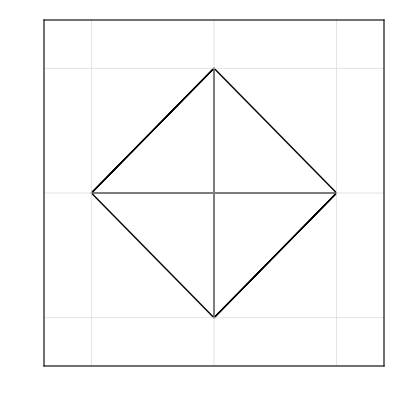
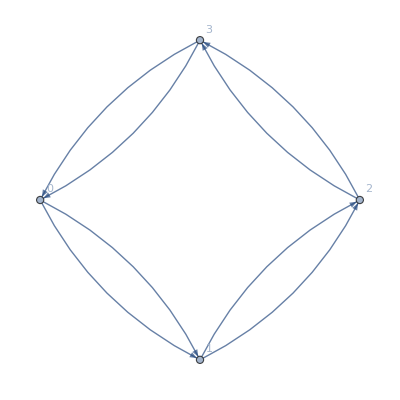
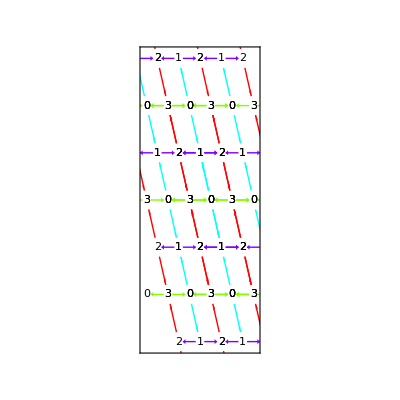

```mathematica
L=2.7;{PlotToricFan[Fan],PlotQuiver[hMat],PlotTiling[hMat,8,{v1,v2},{{-L-.5,L-.5},{-L,L}},.2]}
```

```mathematica
(* recompute height matrix such that h(Phi_{1,2}^1)=h1, h(Phi_{2,3}^1)=h2 *)
hMat=HeightMatrixFromPotential[Wp,Wm,{1,2,1},{2,3,1}]
```

{{{},{h1,-h1+h3/2},{},{}},{{},{},{h2,-h2+h3/2},{}},{{},{},{},{h1,-h1+h3/2}},{{h2,-h2+h3/2},{},{},{}}}

```mathematica
PlotTiling3D[hMat,10,{{1,0,0},{0,1,0},{0,0,1}},5,{}]
```

-Graphics3D-

## Evaluate the partition function of NCDT invariants for framing f={1,0,...} using Quiver Yangian algorithm

```mathematica
Nn=5; (* substitute y=1 to get unrefined, y=-1 to get raw counting *)
Z1=UnrefinedSeriesFromCrystal[hMat,D6Framing[hMat,1],2Nn]
```

1+x_1-2 y x_1 x_2+x_1 x_2^2+4 y^2 x_1 x_2 x_3-4 y^3 x_1 x_2^2 x_3-2 y x_1 x_2 x_3^2+6 y^4 x_1 x_2^2 x_3^2-4 y^3 x_1 x_2^2 x_3^3+x_1 x_2^2 x_3^4-4 y^5 x_1 x_2 x_3 x_4-4 y^7 x_1^2 x_2 x_3 x_4+4 y^6 x_1 x_2^2 x_3 x_4+8 y^10 x_1^2 x_2^2 x_3 x_4-4 y^11 x_1^2 x_2^3 x_3 x_4+4 y^6 x_1 x_2 x_3^2 x_4+4 y^8 x_1^2 x_2 x_3^2 x_4-14 y^9 x_1 x_2^2 x_3^2 x_4-22 y^13 x_1^2 x_2^2 x_3^2 x_4+16 y^16 x_1^2 x_2^3 x_3^2 x_4+16 y^10 x_1 x_2^2 x_3^3 x_4+20 y^14 x_1^2 x_2^2 x_3^3 x_4-24 y^19 x_1^2 x_2^3 x_3^3 x_4-6 y^9 x_1 x_2^2 x_3^4 x_4-6 y^13 x_1^2 x_2^2 x_3^4 x_4+16 y^20 x_1^2 x_2^3 x_3^4 x_4-2 y^9 x_1 x_2 x_3^2 x_4^2-6 y^13 x_1^2 x_2 x_3^2 x_4^2-6 y^15 x_1^3 x_2 x_3^2 x_4^2-2 y^15 x_1^4 x_2 x_3^2 x_4^2+10 y^12 x_1 x_2^2 x_3^2 x_4^2+32 y^18 x_1^2 x_2^2 x_3^2 x_4^2+30 y^22 x_1^3 x_2^2 x_3^2 x_4^2+8 y^24 x_1^4 x_2^2 x_3^2 x_4^2-22 y^21 x_1^2 x_2^3 x_3^2 x_4^2-42 y^27 x_1^3 x_2^3 x_3^2 x_4^2-24 y^15 x_1 x_2^2 x_3^3 x_4^2-60 y^21 x_1^2 x_2^2 x_3^3 x_4^2-44 y^25 x_1^3 x_2^2 x_3^3 x_4^2+68 y^26 x_1^2 x_2^3 x_3^3 x_4^2+15 y^16 x_1 x_2^2 x_3^4 x_4^2+33 y^22 x_1^2 x_2^2 x_3^4 x_4^2-2 y^13 x_1 x_2^2 x_3^2 x_4^3-6 y^21 x_1^2 x_2^2 x_3^2 x_4^3-6 y^27 x_1^3 x_2^2 x_3^2 x_4^3+4 y^24 x_1^2 x_2^3 x_3^2 x_4^3+16 y^18 x_1 x_2^2 x_3^3 x_4^3+60 y^26 x_1^2 x_2^2 x_3^3 x_4^3-20 y^21 x_1 x_2^2 x_3^4 x_4^3-4 y^19 x_1 x_2^2 x_3^3 x_4^4

```mathematica
Zref=NCDTSeriesFromCrystal[hMat,D6Framing[hMat,1],0,0.001,2Nn]
```

1+x_1+(-1/y-y) x_1 x_2+x_1 x_2^2+(2+1/y^2+y^2) x_1 x_2 x_3+(-1/y^3-1/y-y-y^3) x_1 x_2^2 x_3+(-1/y-y) x_1 x_2 x_3^2+(2+1/y^4+1/y^2+y^2+y^4) x_1 x_2^2 x_3^2+(-1/y^3-1/y-y-y^3) x_1 x_2^2 x_3^3+x_1 x_2^2 x_3^4+(-2/y-2 y) x_1 x_2 x_3 x_4+(-2/y-2 y) x_1^2 x_2 x_3 x_4+(2+1/y^2+y^2) x_1 x_2^2 x_3 x_4+(4+2/y^2+2 y^2) x_1^2 x_2^2 x_3 x_4+(-2/y-2 y) x_1^2 x_2^3 x_3 x_4+(2+1/y^2+y^2) x_1 x_2 x_3^2 x_4+(2+1/y^2+y^2) x_1^2 x_2 x_3^2 x_4+(-1/y^5-2/y^3-4/y-4 y-2 y^3-y^5) x_1 x_2^2 x_3^2 x_4+(-3/y^3-8/y-8 y-3 y^3) x_1^2 x_2^2 x_3^2 x_4+(4+2/y^4+4/y^2+4 y^2+2 y^4) x_1^2 x_2^3 x_3^2 x_4+(4+1/y^6+2/y^4+3/y^2+3 y^2+2 y^4+y^6) x_1 x_2^2 x_3^3 x_4+(8+1/y^4+5/y^2+5 y^2+y^4) x_1^2 x_2^2 x_3^3 x_4+(-2/y^5-4/y^3-6/y-6 y-4 y^3-2 y^5) x_1^2 x_2^3 x_3^3 x_4+(-1/y^5-1/y^3-1/y-y-y^3-y^5) x_1 x_2^2 x_3^4 x_4+(-1/y^3-2/y-2 y-y^3) x_1^2 x_2^2 x_3^4 x_4+(4+2/y^4+4/y^2+4 y^2+2 y^4) x_1^2 x_2^3 x_3^4 x_4+(-1/y-y) x_1 x_2 x_3^2 x_4^2+(-1/y^3-2/y-2 y-y^3) x_1^2 x_2 x_3^2 x_4^2+(-1/y^3-2/y-2 y-y^3) x_1^3 x_2 x_3^2 x_4^2+(-1/y-y) x_1^4 x_2 x_3^2 x_4^2+(4+1/y^4+2/y^2+2 y^2+y^4) x_1 x_2^2 x_3^2 x_4^2+(14+1/y^4+8/y^2+8 y^2+y^4) x_1^2 x_2^2 x_3^2 x_4^2+(12+1/y^4+8/y^2+8 y^2+y^4) x_1^3 x_2^2 x_3^2 x_4^2+(2+1/y^4+2/y^2+2 y^2+y^4) x_1^4 x_2^2 x_3^2 x_4^2+(-3/y^3-8/y-8 y-3 y^3) x_1^2 x_2^3 x_3^2 x_4^2+(-6/y^3-15/y-15 y-6 y^3) x_1^3 x_2^3 x_3^2 x_4^2+(-1/y^7-2/y^5-4/y^3-5/y-5 y-4 y^3-2 y^5-y^7) x_1 x_2^2 x_3^3 x_4^2+(-1/y^7-3/y^5-9/y^3-17/y-17 y-9 y^3-3 y^5-y^7) x_1^2 x_2^2 x_3^3 x_4^2+(-1/y^5-6/y^3-15/y-15 y-6 y^3-y^5) x_1^3 x_2^2 x_3^3 x_4^2+(20+2/y^6+7/y^4+15/y^2+15 y^2+7 y^4+2 y^6) x_1^2 x_2^3 x_3^3 x_4^2+(3+1/y^8+1/y^6+2/y^4+2/y^2+2 y^2+2 y^4+y^6+y^8) x_1 x_2^2 x_3^4 x_4^2+(7+1/y^8+2/y^6+4/y^4+6/y^2+6 y^2+4 y^4+2 y^6+y^8) x_1^2 x_2^2 x_3^4 x_4^2+(-1/y-y) x_1 x_2^2 x_3^2 x_4^3+(-1/y^3-2/y-2 y-y^3) x_1^2 x_2^2 x_3^2 x_4^3+(-1/y^3-2/y-2 y-y^3) x_1^3 x_2^2 x_3^2 x_4^3+(2+1/y^2+y^2) x_1^2 x_2^3 x_3^2 x_4^3+(4+1/y^6+2/y^4+3/y^2+3 y^2+2 y^4+y^6) x_1 x_2^2 x_3^3 x_4^3+(16+1/y^8+3/y^6+6/y^4+12/y^2+12 y^2+6 y^4+3 y^6+y^8) x_1^2 x_2^2 x_3^3 x_4^3+(-1/y^9-1/y^7-2/y^5-3/y^3-3/y-3 y-3 y^3-2 y^5-y^7-y^9) x_1 x_2^2 x_3^4 x_4^3+(-1/y^3-1/y-y-y^3) x_1 x_2^2 x_3^3 x_4^4

```mathematica
(Z1/.y->1)-(Zref/.y->1)
```

0

## Construct perfect matchings, and look for pairs of disjoint cuts

```mathematica
Perf=ListPerfectMatchings[Wp,Wm];LiDoubleCuts=Drop[Union[Flatten[Table[If[Intersection[Perf[[i]],Perf[[j]]]=={},{i,j},{}],{i,Length[Perf]},{j,i+1,Length[Perf]}],1]],1]
```

{{1,4},{1,5},{1,6},{1,7},{1,8},{2,3},{2,4},{2,5},{2,6},{2,8},{3,4},{3,5},{3,6},{3,8},{4,7},{4,8},{5,6},{5,7},{6,7},{7,8}}

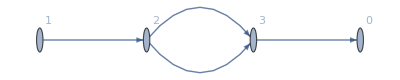
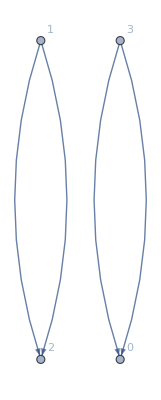
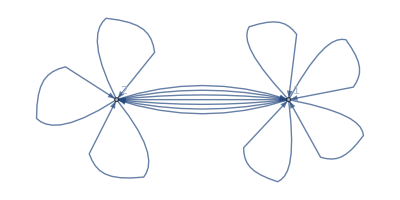
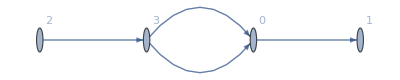
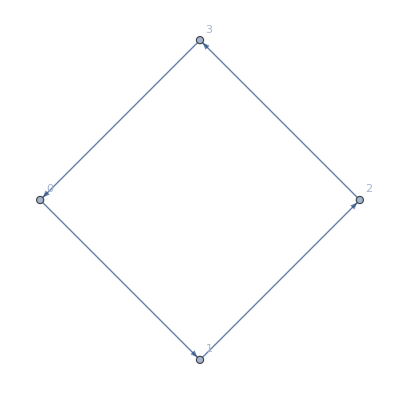
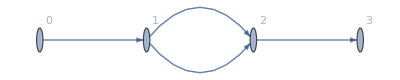
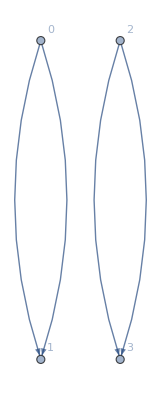
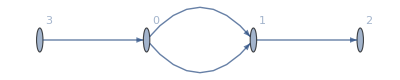
{{{1,4},Graph[{3→4,3→4,4→1,4→1},DirectedEdges→True,VertexLabels→{1→0,2→1,3→2,4→3}],{}},{{1,5},-Graphics-,{}},{{1,6},-Graphics-,{}},{{1,7},-Graphics-,{}},{{1,8},Graph[{2→3,2→3,3→4,3→4},DirectedEdges→True,VertexLabels→{1→0,2→1,3→2,4→3}],{}},{{2,3},-Graphics-,{}},{{2,4},-Graphics-,{}},{{2,5},-Graphics-,{{{1,2,3,4},4}}},{{2,6},-Graphics-,{{{1,2,3,4},4}}},{{2,8},-Graphics-,{}},{{3,4},-Graphics-,{}},{{3,5},-Graphics-,{{{1,2,3,4},4}}},{{3,6},-Graphics-,{{{1,2,3,4},4}}},{{3,8},-Graphics-,{}},{{4,7},Graph[{1→2,1→2,4→1,4→1},DirectedEdges→True,VertexLabels→{1→0,2→1,3→2,4→3}],{}},{{4,8},-Graphics-,{}},{{5,6},-Graphics-,{}},{{5,7},-Graphics-,{}},{{6,7},-Graphics-,{}},{{7,8},Graph[{1→2,1→2,2→3,2→3},DirectedEdges→True,VertexLabels→{1→0,2→1,3→2,4→3}],{}}}

```mathematica
Table[hMat2=Delete[hMat,Perf[[LiDoubleCuts[[i,1]]]]];
hMat3=Delete[hMat2,Perf[[LiDoubleCuts[[i,2]]]]];{LiDoubleCuts[[i]],PlotQuiver[hMat3],ListLoopRCharges[HeightMatrixToDSZ[hMat3],HeightMatrixToDSZ[hMat3]]},{i,Length[LiDoubleCuts]}]
```

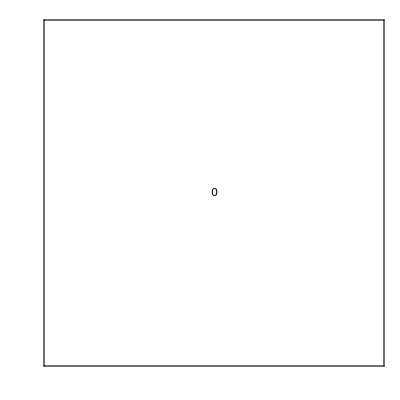
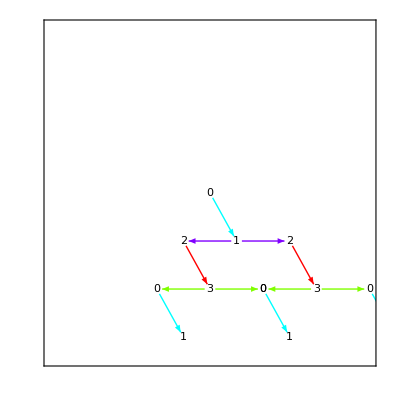
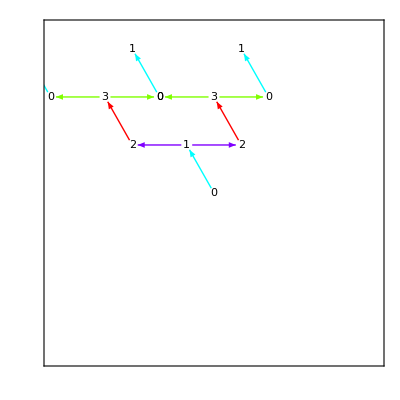
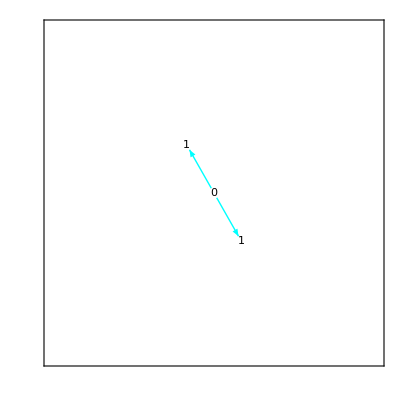
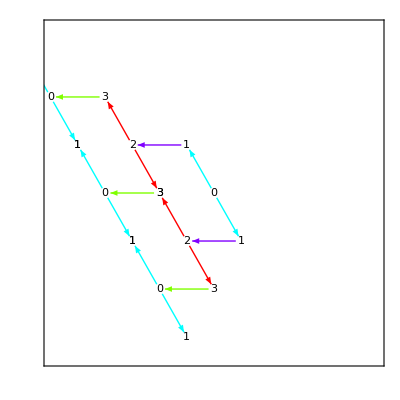
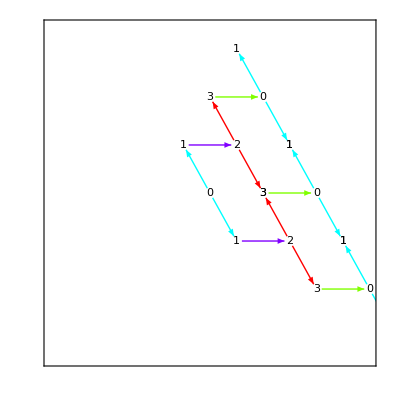
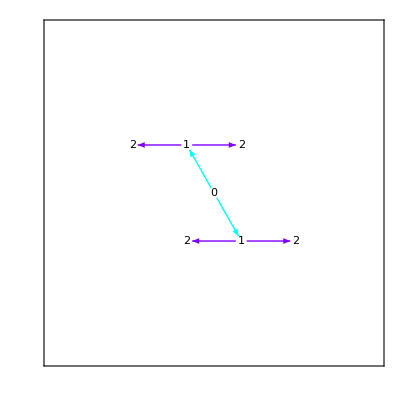
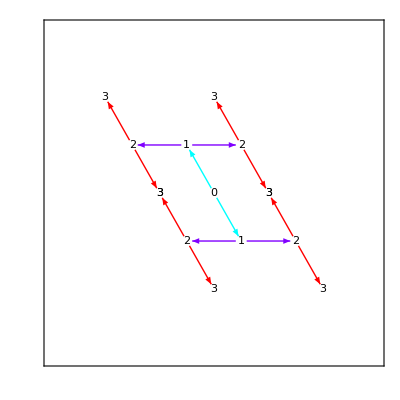
{{{{1,2,1},{1,2,2}},-Graphics-,-Graphics3D-},{{{1,2,1},{3,4,1}},-Graphics-,-Graphics3D-},{{{1,2,2},{3,4,2}},-Graphics-,-Graphics3D-},{{{2,3,1},{2,3,2}},-Graphics-,-Graphics3D-},{{{2,3,1},{4,1,1}},-Graphics-,-Graphics3D-},{{{2,3,2},{4,1,2}},-Graphics-,-Graphics3D-},{{{3,4,1},{3,4,2}},-Graphics-,-Graphics3D-},{{{4,1,1},{4,1,2}},-Graphics-,-Graphics3D-}}

```mathematica
Table[{Perf[[i]],
PlotTiling[hMat,5,{v1,v2},{{-3,3},{-3,3}},.1,Perf[[i]]],PlotTiling3D[hMat,5,{{1,0,0},{0,1,0},{0,0,1}},{{-3,3},{-3,3},{-3,3}},Perf[[i]]]}
,{i,Length[Perf]}]
```